```mathematica
ClearAll
```

ClearAll

```mathematica
ClearAttributes
```

ClearAttributes

```mathematica
ClearCookies
```

ClearCookies

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma1[a_]=gamma055+gammap004n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma1[a];
```

```mathematica
om=0.3;
gamma055=0.55;
gammap004n=-0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points1=Table[{z,omegade[z]},{z,0,1,0.01}]
points5=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.694285},{0.02,0.688541},{0.03,0.682768},{0.04,0.676965},{0.05,0.671134},{0.06,0.665275},{0.07,0.659387},{0.08,0.653471},{0.09,0.647526},{0.1,0.641554},{0.11,0.635554},{0.12,0.629526},{0.13,0.62347},{0.14,0.617388},{0.15,0.611278},{0.16,0.605141},{0.17,0.598978},{0.18,0.592788},{0.19,0.586572},{0.2,0.580329},{0.21,0.574061},{0.22,0.567768},{0.23,0.561449},{0.24,0.555104},{0.25,0.548736},{0.26,0.542342},{0.27,0.535925},{0.28,0.529484},{0.29,0.52302},{0.3,0.516532},{0.31,0.510022},{0.32,0.50349},{0.33,0.496937},{0.34,0.490362},{0.35,0.483766},{0.36,0.477151},{0.37,0.470516},{0.38,0.463862},{0.39,0.45719},{0.4,0.4505},{0.41,0.443794},{0.42,0.437071},{0.43,0.430333},{0.44,0.42358},{0.45,0.416814},{0.46,0.410035},{0.47,0.403244},{0.48,0.396441},{0.49,0.389629},{0.5,0.382809},{0.51,0.37598},{0.52,0.369144},{0.53,0.362304},{0.54,0.355458},{0.55,0.34861},{0.56,0.341761},{0.57,0.334911},{0.58,0.328062},{0.59,0.321215},{0.6,0.314373},{0.61,0.307537},{0.62,0.300708},{0.63,0.293888},{0.64,0.287079},{0.65,0.280282},{0.66,0.2735},{0.67,0.266735},{0.68,0.259988},{0.69,0.253261},{0.7,0.246557},{0.71,0.239877},{0.72,0.233224},{0.73,0.226601},{0.74,0.220009},{0.75,0.213451},{0.76,0.206929},{0.77,0.200447},{0.78,0.194005},{0.79,0.187608},{0.8,0.181258},{0.81,0.174958},{0.82,0.16871},{0.83,0.162517},{0.84,0.156382},{0.85,0.150309},{0.86,0.144301},{0.87,0.138359},{0.88,0.132489},{0.89,0.126692},{0.9,0.120973},{0.91,0.115335},{0.92,0.10978},{0.93,0.104313},{0.94,0.098937},{0.95,0.0936555},{0.96,0.0884724},{0.97,0.0833911},{0.98,0.0784155},{0.99,0.0735493},{1.,0.0687964}}

{{0.,0.3},{0.01,0.305715},{0.02,0.311459},{0.03,0.317232},{0.04,0.323035},{0.05,0.328866},{0.06,0.334725},{0.07,0.340613},{0.08,0.346529},{0.09,0.352474},{0.1,0.358446},{0.11,0.364446},{0.12,0.370474},{0.13,0.37653},{0.14,0.382612},{0.15,0.388722},{0.16,0.394859},{0.17,0.401022},{0.18,0.407212},{0.19,0.413428},{0.2,0.419671},{0.21,0.425939},{0.22,0.432232},{0.23,0.438551},{0.24,0.444896},{0.25,0.451264},{0.26,0.457658},{0.27,0.464075},{0.28,0.470516},{0.29,0.47698},{0.3,0.483468},{0.31,0.489978},{0.32,0.49651},{0.33,0.503063},{0.34,0.509638},{0.35,0.516234},{0.36,0.522849},{0.37,0.529484},{0.38,0.536138},{0.39,0.54281},{0.4,0.5495},{0.41,0.556206},{0.42,0.562929},{0.43,0.569667},{0.44,0.57642},{0.45,0.583186},{0.46,0.589965},{0.47,0.596756},{0.48,0.603559},{0.49,0.610371},{0.5,0.617191},{0.51,0.62402},{0.52,0.630856},{0.53,0.637696},{0.54,0.644542},{0.55,0.65139},{0.56,0.658239},{0.57,0.665089},{0.58,0.671938},{0.59,0.678785},{0.6,0.685627},{0.61,0.692463},{0.62,0.699292},{0.63,0.706112},{0.64,0.712921},{0.65,0.719718},{0.66,0.7265},{0.67,0.733265},{0.68,0.740012},{0.69,0.746739},{0.7,0.753443},{0.71,0.760123},{0.72,0.766776},{0.73,0.773399},{0.74,0.779991},{0.75,0.786549},{0.76,0.793071},{0.77,0.799553},{0.78,0.805995},{0.79,0.812392},{0.8,0.818742},{0.81,0.825042},{0.82,0.83129},{0.83,0.837483},{0.84,0.843618},{0.85,0.849691},{0.86,0.855699},{0.87,0.861641},{0.88,0.867511},{0.89,0.873308},{0.9,0.879027},{0.91,0.884665},{0.92,0.89022},{0.93,0.895687},{0.94,0.901063},{0.95,0.906344},{0.96,0.911528},{0.97,0.916609},{0.98,0.921584},{0.99,0.926451},{1.,0.931204}}

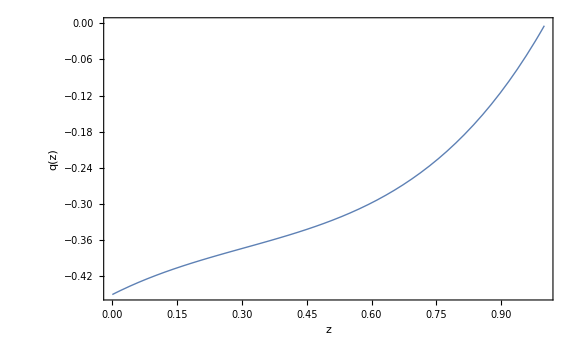

```mathematica
p04n=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma2[a_]=gamma055+gammap002n(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma2[a];
```

```mathematica
om=0.3;
gammap002n=-0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+f[a]/2(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=Fz'[z]/Fz[z] 1/3(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points2=Table[{z,omegade[z]},{z,0,1,0.01}]
points6=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.692853},{0.02,0.685702},{0.03,0.678551},{0.04,0.671402},{0.05,0.664257},{0.06,0.657119},{0.07,0.64999},{0.08,0.642871},{0.09,0.635766},{0.1,0.628675},{0.11,0.621601},{0.12,0.614546},{0.13,0.607511},{0.14,0.600498},{0.15,0.593509},{0.16,0.586545},{0.17,0.579608},{0.18,0.572698},{0.19,0.565818},{0.2,0.558969},{0.21,0.552151},{0.22,0.545367},{0.23,0.538617},{0.24,0.531902},{0.25,0.525223},{0.26,0.518581},{0.27,0.511978},{0.28,0.505413},{0.29,0.498889},{0.3,0.492405},{0.31,0.485962},{0.32,0.479562},{0.33,0.473204},{0.34,0.46689},{0.35,0.460619},{0.36,0.454394},{0.37,0.448213},{0.38,0.442078},{0.39,0.435988},{0.4,0.429946},{0.41,0.42395},{0.42,0.418001},{0.43,0.4121},{0.44,0.406247},{0.45,0.400442},{0.46,0.394686},{0.47,0.388978},{0.48,0.383319},{0.49,0.377709},{0.5,0.372149},{0.51,0.366639},{0.52,0.361178},{0.53,0.355766},{0.54,0.350405},{0.55,0.345094},{0.56,0.339833},{0.57,0.334621},{0.58,0.329461},{0.59,0.32435},{0.6,0.319289},{0.61,0.314279},{0.62,0.309319},{0.63,0.304409},{0.64,0.29955},{0.65,0.29474},{0.66,0.289981},{0.67,0.285271},{0.68,0.280611},{0.69,0.276001},{0.7,0.271441},{0.71,0.266931},{0.72,0.262469},{0.73,0.258057},{0.74,0.253695},{0.75,0.249381},{0.76,0.245116},{0.77,0.2409},{0.78,0.236732},{0.79,0.232613},{0.8,0.228542},{0.81,0.224518},{0.82,0.220543},{0.83,0.216615},{0.84,0.212734},{0.85,0.208901},{0.86,0.205114},{0.87,0.201374},{0.88,0.197681},{0.89,0.194033},{0.9,0.190432},{0.91,0.186876},{0.92,0.183366},{0.93,0.179901},{0.94,0.17648},{0.95,0.173105},{0.96,0.169773},{0.97,0.166486},{0.98,0.163243},{0.99,0.160043},{1.,0.156887}}

{{0.,0.3},{0.01,0.307147},{0.02,0.314298},{0.03,0.321449},{0.04,0.328598},{0.05,0.335743},{0.06,0.342881},{0.07,0.35001},{0.08,0.357129},{0.09,0.364234},{0.1,0.371325},{0.11,0.378399},{0.12,0.385454},{0.13,0.392489},{0.14,0.399502},{0.15,0.406491},{0.16,0.413455},{0.17,0.420392},{0.18,0.427302},{0.19,0.434182},{0.2,0.441031},{0.21,0.447849},{0.22,0.454633},{0.23,0.461383},{0.24,0.468098},{0.25,0.474777},{0.26,0.481419},{0.27,0.488022},{0.28,0.494587},{0.29,0.501111},{0.3,0.507595},{0.31,0.514038},{0.32,0.520438},{0.33,0.526796},{0.34,0.53311},{0.35,0.539381},{0.36,0.545606},{0.37,0.551787},{0.38,0.557922},{0.39,0.564012},{0.4,0.570054},{0.41,0.57605},{0.42,0.581999},{0.43,0.5879},{0.44,0.593753},{0.45,0.599558},{0.46,0.605314},{0.47,0.611022},{0.48,0.616681},{0.49,0.622291},{0.5,0.627851},{0.51,0.633361},{0.52,0.638822},{0.53,0.644234},{0.54,0.649595},{0.55,0.654906},{0.56,0.660167},{0.57,0.665379},{0.58,0.670539},{0.59,0.67565},{0.6,0.680711},{0.61,0.685721},{0.62,0.690681},{0.63,0.695591},{0.64,0.70045},{0.65,0.70526},{0.66,0.710019},{0.67,0.714729},{0.68,0.719389},{0.69,0.723999},{0.7,0.728559},{0.71,0.733069},{0.72,0.737531},{0.73,0.741943},{0.74,0.746305},{0.75,0.750619},{0.76,0.754884},{0.77,0.7591},{0.78,0.763268},{0.79,0.767387},{0.8,0.771458},{0.81,0.775482},{0.82,0.779457},{0.83,0.783385},{0.84,0.787266},{0.85,0.791099},{0.86,0.794886},{0.87,0.798626},{0.88,0.802319},{0.89,0.805967},{0.9,0.809568},{0.91,0.813124},{0.92,0.816634},{0.93,0.820099},{0.94,0.82352},{0.95,0.826895},{0.96,0.830227},{0.97,0.833514},{0.98,0.836757},{0.99,0.839957},{1.,0.843113}}

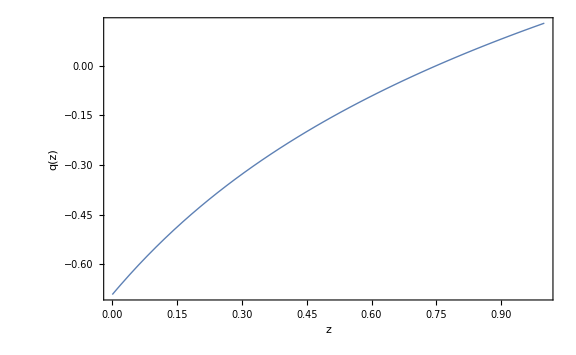

```mathematica
p02n=Plot[q[z],{z,0,1},PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma3[a_]=gamma055+gammap002(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma3[a];
```

```mathematica
om=0.3;
gammap002=0.02;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points3=Table[{z,omegade[z]},{z,0,1,0.01}]
points7=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.690002},{0.02,0.680083},{0.03,0.670251},{0.04,0.660516},{0.05,0.650883},{0.06,0.64136},{0.07,0.631952},{0.08,0.622664},{0.09,0.613501},{0.1,0.604466},{0.11,0.595562},{0.12,0.586792},{0.13,0.578158},{0.14,0.569662},{0.15,0.561306},{0.16,0.553089},{0.17,0.545013},{0.18,0.537078},{0.19,0.529283},{0.2,0.521629},{0.21,0.514115},{0.22,0.50674},{0.23,0.499503},{0.24,0.492402},{0.25,0.485438},{0.26,0.478607},{0.27,0.471909},{0.28,0.465341},{0.29,0.458903},{0.3,0.452592},{0.31,0.446406},{0.32,0.440344},{0.33,0.434402},{0.34,0.42858},{0.35,0.422875},{0.36,0.417285},{0.37,0.411808},{0.38,0.406442},{0.39,0.401185},{0.4,0.396033},{0.41,0.390987},{0.42,0.386042},{0.43,0.381198},{0.44,0.376452},{0.45,0.371802},{0.46,0.367246},{0.47,0.362782},{0.48,0.358408},{0.49,0.354122},{0.5,0.349922},{0.51,0.345806},{0.52,0.341773},{0.53,0.33782},{0.54,0.333946},{0.55,0.330149},{0.56,0.326428},{0.57,0.322779},{0.58,0.319203},{0.59,0.315697},{0.6,0.31226},{0.61,0.308889},{0.62,0.305585},{0.63,0.302344},{0.64,0.299166},{0.65,0.296049},{0.66,0.292992},{0.67,0.289993},{0.68,0.287052},{0.69,0.284166},{0.7,0.281335},{0.71,0.278557},{0.72,0.275832},{0.73,0.273157},{0.74,0.270532},{0.75,0.267956},{0.76,0.265427},{0.77,0.262944},{0.78,0.260507},{0.79,0.258115},{0.8,0.255766},{0.81,0.253459},{0.82,0.251194},{0.83,0.24897},{0.84,0.246785},{0.85,0.244639},{0.86,0.242531},{0.87,0.24046},{0.88,0.238425},{0.89,0.236426},{0.9,0.234462},{0.91,0.232531},{0.92,0.230634},{0.93,0.22877},{0.94,0.226937},{0.95,0.225136},{0.96,0.223365},{0.97,0.221624},{0.98,0.219912},{0.99,0.218228},{1.,0.216573}}

{{0.,0.3},{0.01,0.309998},{0.02,0.319917},{0.03,0.329749},{0.04,0.339484},{0.05,0.349117},{0.06,0.35864},{0.07,0.368048},{0.08,0.377336},{0.09,0.386499},{0.1,0.395534},{0.11,0.404438},{0.12,0.413208},{0.13,0.421842},{0.14,0.430338},{0.15,0.438694},{0.16,0.446911},{0.17,0.454987},{0.18,0.462922},{0.19,0.470717},{0.2,0.478371},{0.21,0.485885},{0.22,0.49326},{0.23,0.500497},{0.24,0.507598},{0.25,0.514562},{0.26,0.521393},{0.27,0.528091},{0.28,0.534659},{0.29,0.541097},{0.3,0.547408},{0.31,0.553594},{0.32,0.559656},{0.33,0.565598},{0.34,0.57142},{0.35,0.577125},{0.36,0.582715},{0.37,0.588192},{0.38,0.593558},{0.39,0.598815},{0.4,0.603967},{0.41,0.609013},{0.42,0.613958},{0.43,0.618802},{0.44,0.623548},{0.45,0.628198},{0.46,0.632754},{0.47,0.637218},{0.48,0.641592},{0.49,0.645878},{0.5,0.650078},{0.51,0.654194},{0.52,0.658227},{0.53,0.66218},{0.54,0.666054},{0.55,0.669851},{0.56,0.673572},{0.57,0.677221},{0.58,0.680797},{0.59,0.684303},{0.6,0.68774},{0.61,0.691111},{0.62,0.694415},{0.63,0.697656},{0.64,0.700834},{0.65,0.703951},{0.66,0.707008},{0.67,0.710007},{0.68,0.712948},{0.69,0.715834},{0.7,0.718665},{0.71,0.721443},{0.72,0.724168},{0.73,0.726843},{0.74,0.729468},{0.75,0.732044},{0.76,0.734573},{0.77,0.737056},{0.78,0.739493},{0.79,0.741885},{0.8,0.744234},{0.81,0.746541},{0.82,0.748806},{0.83,0.75103},{0.84,0.753215},{0.85,0.755361},{0.86,0.757469},{0.87,0.75954},{0.88,0.761575},{0.89,0.763574},{0.9,0.765538},{0.91,0.767469},{0.92,0.769366},{0.93,0.77123},{0.94,0.773063},{0.95,0.774864},{0.96,0.776635},{0.97,0.778376},{0.98,0.780088},{0.99,0.781772},{1.,0.783427}}

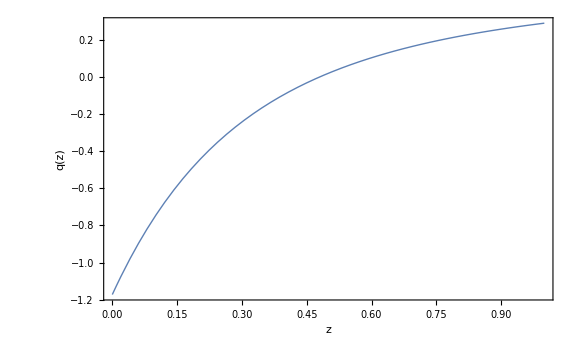

```mathematica
p02=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

```mathematica
1+1
```

2

```mathematica
e[a_]=Sqrt[om/a^3+(1-om)efe[a]];
```

```mathematica
omegam[a_]=om/(a^3 e[a]^2);
```

```mathematica
gamma4[a_]=gamma055+gammap004(1/a-1);
```

```mathematica
f[a_]=omegam[a]^gamma4[a];
```

```mathematica
om=0.3;
gammap004=0.04;
```

```mathematica
sol=NDSolve[{a*f'[a]+f[a]^2+(f[a]/2)(1+a(3/a+(2e'[a])/e[a]))==(3omegam[a])/2, efe[1] == 1}, efe, {a,1/2, 1}];
```

```mathematica
Fa[a_]= efe[a]/.Flatten[sol];
```

```mathematica
Fz[z_]=Fa[1/(1+z)];
```

```mathematica
w[z_]=(Fz'[z]/Fz[z])(1/3)(1+z)-1;
```

```mathematica
ez[z_]=Sqrt[om(1+z)^3+(1-om)Fz[z]];
omegamz[z_]:=om*(1+z)^3/ez[z]^2
omegade[z_]:=(1-om)Fz[z]/ez[z]^2
```

```mathematica
q[z_]:= -1 + (1+z)ez'[z]/ez[z];
```

```mathematica
points4=Table[{z,omegade[z]},{z,0,1,0.01}]
points8=Table[{z,1-omegade[z]},{z,0,1,0.01}]
```

{{0.,0.7},{0.01,0.688584},{0.02,0.677302},{0.03,0.666167},{0.04,0.655191},{0.05,0.644381},{0.06,0.633747},{0.07,0.623295},{0.08,0.61303},{0.09,0.602956},{0.1,0.593078},{0.11,0.583396},{0.12,0.573912},{0.13,0.564629},{0.14,0.555544},{0.15,0.546659},{0.16,0.537972},{0.17,0.529481},{0.18,0.521186},{0.19,0.513082},{0.2,0.505169},{0.21,0.497444},{0.22,0.489902},{0.23,0.482542},{0.24,0.47536},{0.25,0.468353},{0.26,0.461516},{0.27,0.454847},{0.28,0.448342},{0.29,0.441997},{0.3,0.435808},{0.31,0.429772},{0.32,0.423885},{0.33,0.418143},{0.34,0.412544},{0.35,0.407082},{0.36,0.401755},{0.37,0.39656},{0.38,0.391492},{0.39,0.386548},{0.4,0.381726},{0.41,0.377021},{0.42,0.372431},{0.43,0.367953},{0.44,0.363582},{0.45,0.359318},{0.46,0.355156},{0.47,0.351094},{0.48,0.347129},{0.49,0.343258},{0.5,0.339479},{0.51,0.335789},{0.52,0.332186},{0.53,0.328668},{0.54,0.325231},{0.55,0.321874},{0.56,0.318595},{0.57,0.315392},{0.58,0.312262},{0.59,0.309203},{0.6,0.306213},{0.61,0.303292},{0.62,0.300435},{0.63,0.297643},{0.64,0.294913},{0.65,0.292244},{0.66,0.289633},{0.67,0.28708},{0.68,0.284583},{0.69,0.28214},{0.7,0.27975},{0.71,0.277411},{0.72,0.275123},{0.73,0.272883},{0.74,0.270691},{0.75,0.268545},{0.76,0.266445},{0.77,0.264388},{0.78,0.262374},{0.79,0.260402},{0.8,0.25847},{0.81,0.256579},{0.82,0.254726},{0.83,0.25291},{0.84,0.251132},{0.85,0.249389},{0.86,0.247681},{0.87,0.246007},{0.88,0.244367},{0.89,0.242759},{0.9,0.241183},{0.91,0.239637},{0.92,0.238122},{0.93,0.236636},{0.94,0.23518},{0.95,0.233751},{0.96,0.232349},{0.97,0.230974},{0.98,0.229626},{0.99,0.228303},{1.,0.227005}}

{{0.,0.3},{0.01,0.311416},{0.02,0.322698},{0.03,0.333833},{0.04,0.344809},{0.05,0.355619},{0.06,0.366253},{0.07,0.376705},{0.08,0.38697},{0.09,0.397044},{0.1,0.406922},{0.11,0.416604},{0.12,0.426088},{0.13,0.435371},{0.14,0.444456},{0.15,0.453341},{0.16,0.462028},{0.17,0.470519},{0.18,0.478814},{0.19,0.486918},{0.2,0.494831},{0.21,0.502556},{0.22,0.510098},{0.23,0.517458},{0.24,0.52464},{0.25,0.531647},{0.26,0.538484},{0.27,0.545153},{0.28,0.551658},{0.29,0.558003},{0.3,0.564192},{0.31,0.570228},{0.32,0.576115},{0.33,0.581857},{0.34,0.587456},{0.35,0.592918},{0.36,0.598245},{0.37,0.60344},{0.38,0.608508},{0.39,0.613452},{0.4,0.618274},{0.41,0.622979},{0.42,0.627569},{0.43,0.632047},{0.44,0.636418},{0.45,0.640682},{0.46,0.644844},{0.47,0.648906},{0.48,0.652871},{0.49,0.656742},{0.5,0.660521},{0.51,0.664211},{0.52,0.667814},{0.53,0.671332},{0.54,0.674769},{0.55,0.678126},{0.56,0.681405},{0.57,0.684608},{0.58,0.687738},{0.59,0.690797},{0.6,0.693787},{0.61,0.696708},{0.62,0.699565},{0.63,0.702357},{0.64,0.705087},{0.65,0.707756},{0.66,0.710367},{0.67,0.71292},{0.68,0.715417},{0.69,0.71786},{0.7,0.72025},{0.71,0.722589},{0.72,0.724877},{0.73,0.727117},{0.74,0.729309},{0.75,0.731455},{0.76,0.733555},{0.77,0.735612},{0.78,0.737626},{0.79,0.739598},{0.8,0.74153},{0.81,0.743421},{0.82,0.745274},{0.83,0.74709},{0.84,0.748868},{0.85,0.750611},{0.86,0.752319},{0.87,0.753993},{0.88,0.755633},{0.89,0.757241},{0.9,0.758817},{0.91,0.760363},{0.92,0.761878},{0.93,0.763364},{0.94,0.76482},{0.95,0.766249},{0.96,0.767651},{0.97,0.769026},{0.98,0.770374},{0.99,0.771697},{1.,0.772995}}

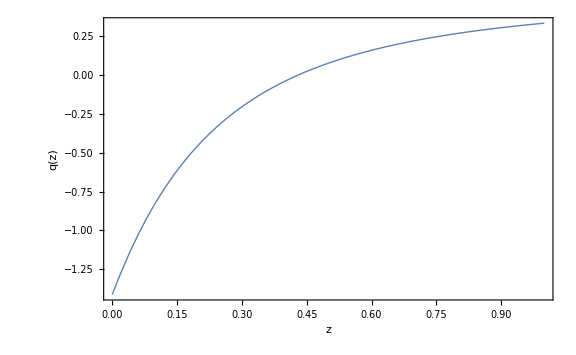

```mathematica
p04=Plot[q[z],{z,0,1}, PlotStyle->Thick, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24],Style["q(z)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}]
```

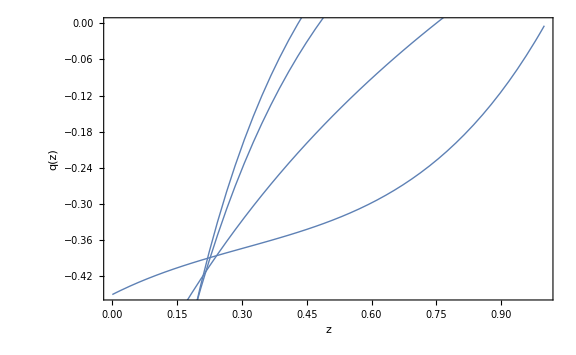

```mathematica
Show[p04n, p02n, p02, p04]
```

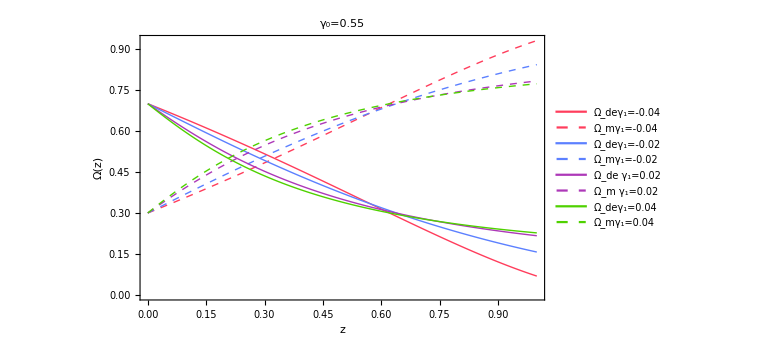

```mathematica
list2=ListLinePlot[{points1,points5,points2, points6, points3, points7, points4, points8}, PlotStyle->{{Thick, RGBColor[1,0.24,0.36]}, {Thick,Dashed, RGBColor[1,0.24,0.36]},{Thick, RGBColor[0.36,0.5,1]}, {Thick,Dashed, RGBColor[0.36,0.5,1]},{Thick, RGBColor[0.68,0.22,0.72]}, {Thick,Dashed, RGBColor[0.68,0.22,0.72]},{Thick, RGBColor[0.31,0.82,0]}, {Thick, Dashed,RGBColor[0.31,0.82,0]}}, ImageSize->Large,Frame ->True,FrameLabel->{Style["z", Black, FontSize->24,  FontFamily->"Helvetica"],Style["Ω(z)", Black, FontSize->24,  FontFamily->"Helvetica"]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, PlotLegends->Placed[LineLegend[{"Ω_deγ_1=-0.04","Ω_mγ_1=-0.04", "Ω_deγ_1=-0.02","Ω_mγ_1=-0.02", "Ω_de γ_1=0.02", "Ω_m γ_1=0.02","Ω_deγ_1=0.04", "Ω_mγ_1=0.04"}, Background->White, LabelStyle->{FontSize->7}, LegendMarkerSize->{{20,10}}],{Right, Center}], PlotLabel->Style["γ_0=0.55", Black, FontSize->20,  FontFamily->"Helvetica"], Axes->False]
```

```mathematica
SetDirectory["C:\\Users\\Gerald\\Desktop\\7sem\\dark energy\\plots_paper"]
```

C:\Users\Gerald\Desktop\7sem\dark energy\plots_paper

```mathematica
Export["omega(z).pdf",list2,ImageResolution->500]
```

omega(z).pdf